```mathematica
ResourceFunction["HydrogenWavefunction"][{1,0,0},a,{r,θ,ϕ}]
```

(√(1/a^3) ⅇ^(-r/a))/(√π)

```mathematica
f[r_]:= ⅇ^-r/(√π)
```

```mathematica
Laplacian[f[r],{r, θ, ϕ}, "Spherical" ]
```

ⅇ^-r/(√π)-(2 ⅇ^-r)/(√π r)

```mathematica
Hpsi = -1/2 Laplacian[f[r],{r, θ, ϕ}, "Spherical" ]- 1/r f[r]
```

1/2 (-ⅇ^-r/(√π)+(2 ⅇ^-r)/(√π r))-ⅇ^-r/(√π r)

Check limits

```mathematica
Limit[1/2 (-ⅇ^-r/(√π)+(2 ⅇ^-r)/(√π r)), r-> 0, Direction->"FromAbove"]
Limit[-ⅇ^-r/(√π r), r-> 0, Direction->"FromAbove"]
```

∞

-∞

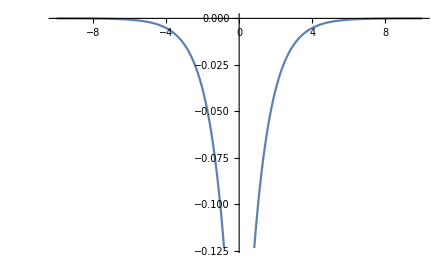

```mathematica
Plot[1/2 (-ⅇ^(-Abs[x])/(√π)+(2 ⅇ^(-Abs[x]))/(√π Abs[x]))-ⅇ^(-Abs[x])/(√π Abs[x]), {x, -10, 10}]
```

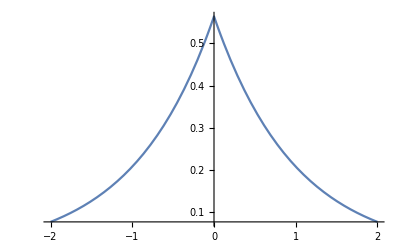

```mathematica
Plot[ⅇ^(-Abs[x])/(√π), {x, -2,2}]
```

```mathematica
"interactive plot"%28DynamicModule[{xc,dx},Manipulate[Plot[1/2 (-ⅇ^-r/(√π)+(2 ⅇ^-r)/(√π r))-ⅇ^-r/(√π r),{r,xc-dx,xc+dx}],{{xc,5,"center"},-25,35},{{dx,5.,"zoom"},30,0.3}],DynamicModuleValues:>{}]
```